```mathematica
Quit[];
```

```mathematica
$LoadAddOns = {"FeynArts","FeynHelpers"};
<< FeynCalc`
$FAVerbose = 0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Photonless_Weak_gaugeonly_FA","Photonless_Weak_gaugeonly_FA.nlo"}]]
```

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA"}]]
```

Successfully patched FeynArts.

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,k1,k2,Mu,Mu,Mc,Mc];
```

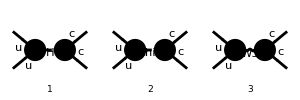

```mathematica
TreeDiags = InsertFields[CreateTopologies[0, 2-> 2, ExcludeTopologies->{}],{F[1],-F[1]} ->{ F[2],-F[2]}, InsertionLevel->{Particles},  Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}]];
Paint[TreeDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{3,1},ImageSize->{300,100}];
```

```mathematica
AmpTree[0]=FCReplaceAll[#,vH->2 mW/gW,lambda->mh^2 gW^2/(8 mW^2),yu1->Mu gW/(Sqrt[2] mW),yu2->Mc gW/(Sqrt[2] mW)]&/@Contract/@FCFAConvert[CreateFeynAmp[TreeDiags,Truncated->False,PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings]//Total//DiracSubstitute67//Simplify//Expand//FeynAmpDenominatorExplicit;
```

```mathematica
uuh=InsertFields[CreateTopologies[0, 2-> 1, ExcludeTopologies->{}],{F[1],-F[1]} ->S[1], InsertionLevel->{Particles},  Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}]]//FCFAConvert[CreateFeynAmp[#,Truncated->True,PreFactor->1],IncomingMomenta->p,OutgoingMomenta->{q,r},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings]&//Total//ReplaceAll[#,{yu1->Mu gW/(Sqrt[2] mW),yu2->Mc gW/(Sqrt[2] mW)}]&;
hcc=InsertFields[CreateTopologies[0, 1-> 2, ExcludeTopologies->{}],S[1]->{F[2],-F[2]} , InsertionLevel->{Particles},  Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}]]//FCFAConvert[CreateFeynAmp[#,Truncated->True,PreFactor->1],IncomingMomenta->{p,q},OutgoingMomenta->{r},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings]&//Total//ReplaceAll[#,{yu1->Mu gW/(Sqrt[2] mW),yu2->Mc gW/(Sqrt[2] mW)}]&;
uuW=InsertFields[CreateTopologies[0, 2-> 1, ExcludeTopologies->{}],{F[1],-F[1]} ->V[3], InsertionLevel->{Particles},  Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}]]//FCFAConvert[CreateFeynAmp[#,Truncated->True,PreFactor->1],IncomingMomenta->p,OutgoingMomenta->{q,r},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings]&//Total//ReplaceAll[#,{yu1->Mu gW/(Sqrt[2] mW),yu2->Mc gW/(Sqrt[2] mW)}]&;
Wcc=InsertFields[CreateTopologies[0, 1-> 2, ExcludeTopologies->{}],V[3]->{F[2],-F[2]}, InsertionLevel->{Particles},Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}]]//FCFAConvert[CreateFeynAmp[#,Truncated->True,PreFactor->1],IncomingMomenta->{p,q},OutgoingMomenta->r,ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings]&//Total//ReplaceAll[#,Lor1->Lor2]&//ReplaceAll[#,{yu1->Mu gW/(Sqrt[2] mW),yu2->Mc gW/(Sqrt[2] mW)}]&;
uuchi=InsertFields[CreateTopologies[0, 2-> 1, ExcludeTopologies->{}],{F[1],-F[1]} ->S[4], InsertionLevel->{Particles},  Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}]]//FCFAConvert[CreateFeynAmp[#,Truncated->True,PreFactor->1],IncomingMomenta->p,OutgoingMomenta->{q,r},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings]&//DiracSubstitute67//Simplify//Total//ReplaceAll[#,{yu1->Mu gW/(Sqrt[2] mW),yu2->Mc gW/(Sqrt[2] mW)}]&;
chicc=InsertFields[CreateTopologies[0, 1-> 2, ExcludeTopologies->{}],S[4]->{F[2],-F[2]}, InsertionLevel->{Particles},  Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}]]//FCFAConvert[CreateFeynAmp[#,Truncated->True,PreFactor->1],IncomingMomenta->{p,q},OutgoingMomenta->r,ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings]&//DiracSubstitute67//Simplify//Total//ReplaceAll[#,{yu1->Mu gW/(Sqrt[2] mW),yu2->Mc gW/(Sqrt[2] mW)}]&;
```

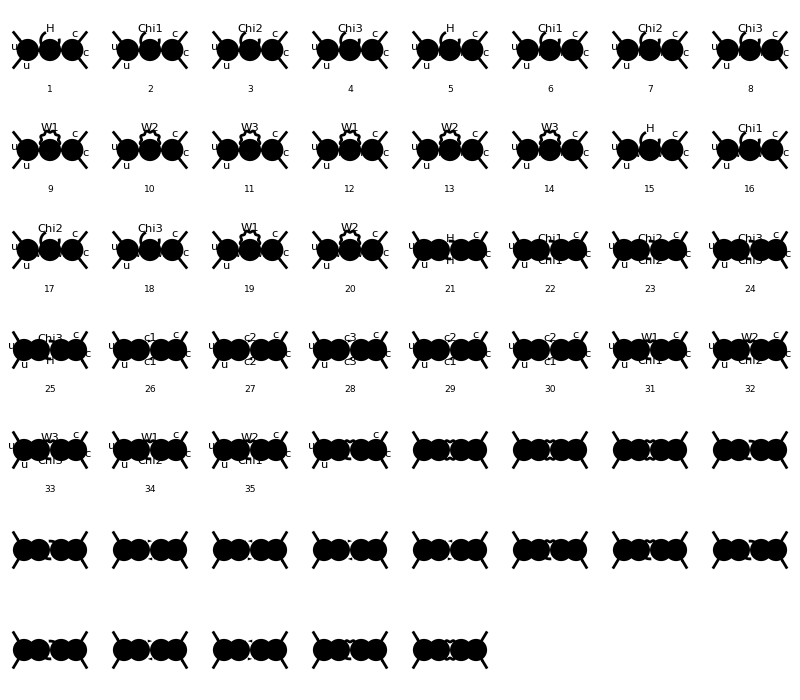

```mathematica
LoopDiags = InsertFields[CreateTopologies[1, 2-> 2, ExcludeTopologies->{Tadpoles,WFCorrections}],{F[1],-F[1]} ->{ F[2],-F[2]}, InsertionLevel->{Particles},ExcludeParticles->{F[1],F[2],F[3],F[4]},  Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}]];
Paint[LoopDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{8,7},ImageSize->{800,700}];
```

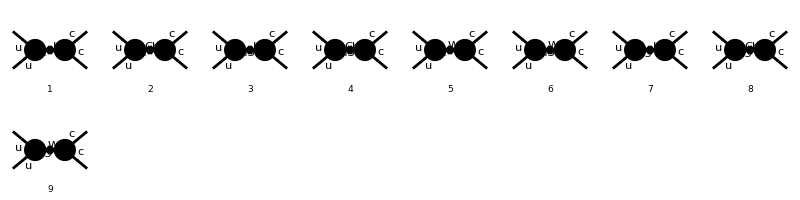

```mathematica
CTDiags = InsertFields[CreateCTTopologies[1, 2 -> 2,ExcludeTopologies->{Tadpoles,WFCorrectionCTs}],{F[1],-F[1]} ->{ F[2],-F[2]}, InsertionLevel->{Particles}, Model -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Photonless_Weak_twogenerations_FA", "Photonless_Weak_twogenerations_FA"}]];
Paint[DiagramExtract[CTDiags,7..15], Numbering->Simple, SheetHeader->None,ColumnsXRows->{8,2},ImageSize->{800,200}];
```

```mathematica
Const1[x_]:=1;
Const0[x_]:=0;
evalLoop[ex_]:=ex//TID[#,q,ToPaVe->True]&//DotSimplify[#,Expanding->False]&//DiracSimplify[#,DiracSubstitute67->True]&//Collect2[#,{A0,B0,C0,D0}]&;
processLoop[exs_]:=(
a1=FCTraceFactor/@DotSimplify[#,Expanding->False]&/@exs;
a2=evalLoop/@a1;
a3=Total[a2];
a4=ChangeDimension[PaXEvaluate[a3],4]//Expand
)
```

```mathematica
AmpLoop[0]=FCReplaceAll[#,vH->2 mW/gW,lambda->mh^2 gW^2/(8 mW^2),yu1->Mu gW/(Sqrt[2] mW),yu2->Mc gW/(Sqrt[2] mW)]&/@Contract/@FCFAConvert[CreateFeynAmp[LoopDiags,Truncated->False,PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings];
```

```mathematica
CTHH=(Simplify[(2π)^4 Spinor[Momentum[k1,D],Mc,1].(-hcc).Spinor[-Momentum[k2,D],Mc,1]Refine[(R2$vertlist[[1]][[2]]+UV$vertlist[[1]][[2]]/.{FR$Eps->Epsilon,FR$MU->ScaleMu,lambda->mh^2 gW^2/(8 mW^2),vH->2 mW/gW}),Assumptions->{mW>mh>0,ScaleMu>0}]Spinor[-Momentum[p2,D],Mu,1].uuh.Spinor[Momentum[p1,D],Mu,1],Assumptions->ScaleMu>0]/.{SP[2,2]->s})//Expand//Collect2[#,1/Epsilon]&;
CTChiChi=(Simplify[(2π)^4 Spinor[Momentum[k1,D],Mc,1].(-chicc).Spinor[-Momentum[k2,D],Mc,1]Refine[(R2$vertlist[[4]][[2]]+UV$vertlist[[4]][[2]]/.{FR$Eps->Epsilon,FR$MU->ScaleMu,lambda->mh^2 gW^2/(8 mW^2),vH->2 mW/gW}),Assumptions->{mW>mh>0,ScaleMu>0}]Spinor[-Momentum[p2,D],Mu,1].uuchi.Spinor[Momentum[p1,D],Mu,1],Assumptions->ScaleMu>0]/.{SP[2,2]->s})//Expand//Collect2[#,1/Epsilon]&;
CTWW=(Simplify[(2π)^4 Spinor[Momentum[k1,D],Mc,1].(-Wcc).Spinor[-Momentum[k2,D],Mc,1]Refine[(R2$vertlist[[7]][[2]]+UV$vertlist[[7]][[2]]/.{FR$Eps->Epsilon,FR$MU->ScaleMu,lambda->mh^2 gW^2/(8 mW^2),vH->2 mW/gW,ME[Index[Lorentz,Ext[1]],Index[Lorentz,Ext[2]]]->Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]],FV[2,Index[Lorentz,Ext[1]]]->Pair[LorentzIndex[Lor1],Momentum[p1]]+Pair[LorentzIndex[Lor1],Momentum[p2]],FV[2,Index[Lorentz,Ext[2]]]->Pair[LorentzIndex[Lor2],Momentum[p1]]+Pair[LorentzIndex[Lor2],Momentum[p2]]}),Assumptions->{mW>mh>0,ScaleMu>0}]Spinor[-Momentum[p2,D],Mu,1].uuW.Spinor[Momentum[p1,D],Mu,1],Assumptions->ScaleMu>0]/.{SP[2,2]->s})//Expand//Collect2[#,1/Epsilon]&;
```

```mathematica
AmpLoop[1]=AmpLoop[0]//processLoop;
```

Get::noopen: Cannot open C:\Users\hypercube256\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

```mathematica
AmpTotal[0]=((AmpLoop[1]+AmpTree[0]+CTHH+CTChiChi+CTWW)/.ScaleMu->1)//Expand;
```

```mathematica
AmpTotal[1]=((AmpTotal[0]/.(1/Epsilon)->0)/.(Epsilon->0))//Simplify;
```

```mathematica
AmpTotal[2]=AmpTotal[1]/.{gW->0.3,mW->1,mh->0.1}//FeynAmpDenominatorExplicit;
```

```mathematica
AmpTotal[2]
```

1/(0.01-s)62.5783 ((-2.4647×10^-16+0.0124039 ⅈ) s^2+(9.81389×10^-18+0.0212216 ⅈ) s-(0.+9.80518×10^-6 ⅈ) (0.01-s)-(7.34919×10^-20-0.0157665 ⅈ)) (φ(k1,Mc)).((0.-0.15 ⅈ) Mc).(φ(-k2,Mc)) (φ(-p2,Mu)).((0.-0.15 ⅈ) Mu).(φ(p1,Mu))+1/1152 ⅈ (-1/(1-s)4.01003 (1.61899 (1-s) (1.×10^-6 (4-3 s)+0.07 (7-3 s)+15 s+0.0001 (15 s-23)-63)-3.99 (-102.85 s^2+287.954 s-0.733855 (1-s)-113.104)) (φ(k1,Mc)).(-0.15 Mc (γ̄)^5).(φ(-k2,Mc)) (φ(-p2,Mu)).(-0.15 Mu (γ̄)^5).(φ(p1,Mu))+(25.92 (φ(k1,Mc)).γ^Lor1.(1/2-(γ̄)^5/2).(φ(-k2,Mc)) (φ(-p2,Mu)).γ^Lor1.(1/2-(γ̄)^5/2).(φ(p1,Mu)))/(1-s)+0.888264 (-(14.7715 (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(φ(OverBar[p1],Mu)))/((s-1)^2 s)+(8.946 (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(φ(OverBar[p1],Mu)))/(s-1)^2+(14.7715 (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(φ(OverBar[p1],Mu)))/((s-1)^2 s)-(8.946 (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(φ(OverBar[p1],Mu)))/(s-1)^2+1/((s-1)^2 s)6.48 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(φ(-OverBar[k2],Mc)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(φ(OverBar[p1],Mu))-1/((s-1)^2 s)6.48 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(γ̄)^5.(φ(-OverBar[k2],Mc)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(φ(OverBar[p1],Mu))+(10.0728 s (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(φ(OverBar[p1],Mu)))/(s-1)^2-(30.9564 (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(φ(OverBar[p1],Mu)))/(s-1)^2+(0.150149 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(φ(OverBar[p1],Mu)))/(s-1)^2+(0.179104 (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(φ(OverBar[p1],Mu)))/(s-1)^2+(1.39355 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)))/(s-1)^2+(4.25907 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)))/((s-1)^2 s)-(3.67704 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)))/(s-1)^2-(1.20647 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)))/((s-1)^2 s^2)-(0.150149 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(φ(OverBar[p1],Mu)))/(s-1)^2-(0.179104 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(φ(OverBar[p1],Mu)))/(s-1)^2-(0.150149 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(φ(OverBar[p1],Mu)))/(s-1)^2-(0.179104 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(φ(OverBar[p1],Mu)))/(s-1)^2-(2.81851 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(φ(OverBar[p1],Mu)))/(s-1)^2+(27.711 (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(φ(OverBar[p1],Mu)))/(s-1)^2-(10.0728 s (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2+(30.9564 (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2-(0.150149 s (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2-(0.179104 (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2-(1.39355 s (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2-(4.25907 (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/((s-1)^2 s)+(3.67704 (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2+(1.20647 (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/((s-1)^2 s^2)+(0.150149 s (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2+(0.179104 (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2+(0.150149 s (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2+(0.179104 (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2+(2.81851 s (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2-(27.711 (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(-OverBar[k2],Mc)))/(s-1)^2+(14.7715 (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(γ̄)^5.(φ(OverBar[p1],Mu)))/((s-1)^2 s)-(8.946 (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(14.7715 (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(γ̄)^5.(φ(OverBar[p1],Mu)))/((s-1)^2 s)+(8.946 (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(10.0728 s (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2+(30.9564 (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2+(10.0728 s (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(30.9564 (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(0.150149 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(0.179104 (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2+(0.150149 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2+(0.179104 (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(1.39355 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(4.25907 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)))/((s-1)^2 s)+(3.67704 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2+(1.20647 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)))/((s-1)^2 s^2)+(1.39355 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2+(4.25907 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)))/((s-1)^2 s)-(3.67704 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(1.20647 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)))/((s-1)^2 s^2)+(0.150149 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2+(0.179104 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(0.150149 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(0.179104 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2+(0.150149 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2+(0.179104 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(0.150149 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(0.179104 (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2+(2.81851 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(27.711 (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(2.81851 s (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2+(27.711 (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(OverBar[p1],Mu)))/(s-1)^2-(12.96 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)-(25.92 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2-(2.16 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)+(0.54 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2+(2.16 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)-(0.54 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2+(2.16 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)-(0.54 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2-(21.6 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)+(5.4 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2+(12.96 √((s-4) s) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(γ̄)^5.(φ(-OverBar[k2],Mc)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)+(25.92 √((s-4) s) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(γ̄)^5.(φ(-OverBar[k2],Mc)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2+(2.16 √((s-4) s) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(-OverBar[k2],Mc)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)-(0.54 √((s-4) s) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(-OverBar[k2],Mc)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2-(2.16 √((s-4) s) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(-OverBar[k2],Mc)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)+(0.54 √((s-4) s) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(-OverBar[k2],Mc)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2-(2.16 √((s-4) s) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(-OverBar[k2],Mc)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)+(0.54 √((s-4) s) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(-OverBar[k2],Mc)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2+(21.6 √((s-4) s) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(-OverBar[k2],Mc)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)-(5.4 √((s-4) s) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(-OverBar[k2],Mc)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2+(12.96 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)+(25.92 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2-(12.96 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)-(25.92 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^Lor2.(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor2.(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2+(2.16 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)-(0.54 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2-(2.16 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)+(0.54 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($3839)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2-(2.16 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)+(0.54 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2+(2.16 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)-(0.54 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4526)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2-(2.16 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)+(0.54 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2+(2.16 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)-(0.54 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4806)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2+(21.6 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)-(5.4 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2-(21.6 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/((s-1)^2 s)+(5.4 √((s-4) s) (φ(OverBar[k1],Mc)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($5402)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(1/2 (-s+√((s-4) s)+2)))/(s-1)^2+1/((s-0.01)^2 s)3.24 Mc Mu (φ(OverBar[k1],Mc)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(φ(OverBar[p1],Mu)) (12 log(4 π) s^2-24 log(2 π) s^2-12 ℽ s^2+24 s^2+12 √((s-4) s) log(1/2 (-s+√((s-4) s)+2)) s-54 log(4 π) s+108 log(2 π) s-22.8141 s-36.0003 √((s-4) s) log(1/2 (-s+√((s-4) s)+2))-0.0009 √((s-0.04) s) log(50. (-s+√((s-0.04) s)+0.02)))-1/((s-1)^2 s)1.0908 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))+1/(s-1)^2 0.54 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))+1/((s-1)^2 s^2)0.529254 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))+1/((s-1)^2 s)1.0908 √((1-s)^2-0.02 (s+1)+0.0001) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))-1/(s-1)^2 0.54 √((1-s)^2-0.02 (s+1)+0.0001) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))-1/((s-1)^2 s^2)0.529254 √((1-s)^2-0.02 (s+1)+0.0001) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(φ(OverBar[p1],Mu)) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))-1/((s-1)^2 s)6.48 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(γ̄)^5.(φ(OverBar[p1],Mu)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))+1/((s-1)^2 s)6.48 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^Lor1.(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^Lor1.(γ̄)^5.(φ(OverBar[p1],Mu)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))+1/((s-1)^2 s)1.0908 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))-1/(s-1)^2 0.54 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))-1/((s-1)^2 s^2)0.529254 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))-1/((s-1)^2 s)1.0908 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))+1/(s-1)^2 0.54 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))+1/((s-1)^2 s^2)0.529254 √((1-s)^2-0.02 (s+1)+0.0001) (φ(OverBar[k1],Mc)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (φ(-OverBar[p2],Mu)).(γ̄)^($AL($4179)).(γ̄)^5.(φ(OverBar[p1],Mu)) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))+1/((s-1)^2 s^3)0.54 Mc (φ(OverBar[k1],Mc)).(γ̄)^5.(φ(-OverBar[k2],Mc)) (2 Mu s (φ(-OverBar[p2],Mu)).(γ̄)^5.(φ(OverBar[p1],Mu)) (-36 log(4 π) s^3+72 log(2 π) s^3-70.8513 s^3-24 √((s-4) s) log(1/2 (-s+√((s-4) s)+2)) s^2-12 √((1-s)^2-0.02 (s+1)+0.0001) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01)) s^2+60 log(4 π) s^2-120 log(2 π) s^2+67.5633 s^2+0.138155 (2 s+0.01 (s+2)-2) s-12 √((s-4) s) log(1/2 (-s+√((s-4) s)+2)) s+23.8806 √((1-s)^2-0.02 (s+1)+0.0001) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01)) s-69.8984 s-5.8806 √((1-s)^2-0.02 (s+1)+0.0001) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))+13.4052)-((φ(-OverBar[p2],Mu)).(γ̄·OverBar[k1]).(φ(OverBar[p1],Mu))+(φ(-OverBar[p2],Mu)).(γ̄·OverBar[k2]).(φ(OverBar[p1],Mu))-(φ(-OverBar[p2],Mu)).(γ̄·OverBar[k1]).(γ̄)^5.(φ(OverBar[p1],Mu))-(φ(-OverBar[p2],Mu)).(γ̄·OverBar[k2]).(γ̄)^5.(φ(OverBar[p1],Mu))) (70 log(4 π) s^3-140 log(2 π) s^3+17.5432 s^3+90 √((s-4) s) log(1/2 (-s+√((s-4) s)+2)) s^2-20 √((1-s)^2-0.02 (s+1)+0.0001) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01)) s^2+222.435 s^2+0.0921034 (0.01 (4-3 s)+s-4) s+72 √((s-4) s) log(1/2 (-s+√((s-4) s)+2)) s+9.9206 √((1-s)^2-0.02 (s+1)+0.0001) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01)) s-48.5095 s-7.8408 √((1-s)^2-0.02 (s+1)+0.0001) log(5. (-s+√((1-s)^2-0.02 (s+1)+0.0001)+1.01))+17.8736))+162.15 s (φ(k1,Mc)).((0.+0.15 ⅈ) γ^Lor2.(γ̄)^7).(φ(-k2,Mc)) (φ(-p2,Mu)).((0.+0.15 ⅈ) γ^Lor1.(γ̄)^7).(φ(p1,Mu)) (ḡ)^Lor1Lor2-1318.68 (φ(k1,Mc)).((0.+0.15 ⅈ) γ^Lor2.(γ̄)^7).(φ(-k2,Mc)) (φ(-p2,Mu)).((0.+0.15 ⅈ) γ^Lor1.(γ̄)^7).(φ(p1,Mu)) (ḡ)^Lor1Lor2-768 (φ(k1,Mc)).((0.+0.15 ⅈ) γ^Lor2.(γ̄)^7).(φ(-k2,Mc)) (φ(-p2,Mu)).((0.+0.15 ⅈ) γ^Lor1.(γ̄)^7).(φ(p1,Mu)) OverBar[p1]^Lor1 OverBar[p1]^Lor2-768 (φ(k1,Mc)).((0.+0.15 ⅈ) γ^Lor2.(γ̄)^7).(φ(-k2,Mc)) (φ(-p2,Mu)).((0.+0.15 ⅈ) γ^Lor1.(γ̄)^7).(φ(p1,Mu)) OverBar[p2]^Lor1 OverBar[p1]^Lor2-768 (φ(k1,Mc)).((0.+0.15 ⅈ) γ^Lor2.(γ̄)^7).(φ(-k2,Mc)) (φ(-p2,Mu)).((0.+0.15 ⅈ) γ^Lor1.(γ̄)^7).(φ(p1,Mu)) OverBar[p1]^Lor1 OverBar[p2]^Lor2-768 (φ(k1,Mc)).((0.+0.15 ⅈ) γ^Lor2.(γ̄)^7).(φ(-k2,Mc)) (φ(-p2,Mu)).((0.+0.15 ⅈ) γ^Lor1.(γ̄)^7).(φ(p1,Mu)) OverBar[p2]^Lor1 OverBar[p2]^Lor2+0.))

```mathematica
AmpSq[0]=AmpTotal[2](ComplexConjugate[AmpTotal[2]])//FermionSpinSum[#,ExtraFactor->1/4]&
```

FermionSpinSum::spinorsleft: Error! After applying FermionSpinSum to all spinor chains the output still contains spinors.